#### Define styling function

```mathematica
style[x_,n_]:=Style[x,FontFamily->"EB Garamond",FontSize->n]
```

#### Set up Lorenz’s equations and solve them

```mathematica
eq1=x'[t]==σ(y[t]-x[t])
eq2=y'[t]==r x[t] - y[t] - x[t] z[t]
eq3=z'[t]==x [t]y[t]-b z[t]
```

x'[t]==σ (-x[t]+y[t])

y'[t]==r x[t]-y[t]-x[t] z[t]

z'[t]==x[t] y[t]-b z[t]

### Solve using Lorenz parameters

#### Lorenz parameters

```mathematica
sol1=With[{σval=10,bval=8/3,rval=28},NDSolve[{eq1,eq2,eq3,x[0]==0,y[0]==1,z[0]==0}/.{r->rval,σ->σval,b->bval},{x,y,z},{t,0,100}]][[1]];
```

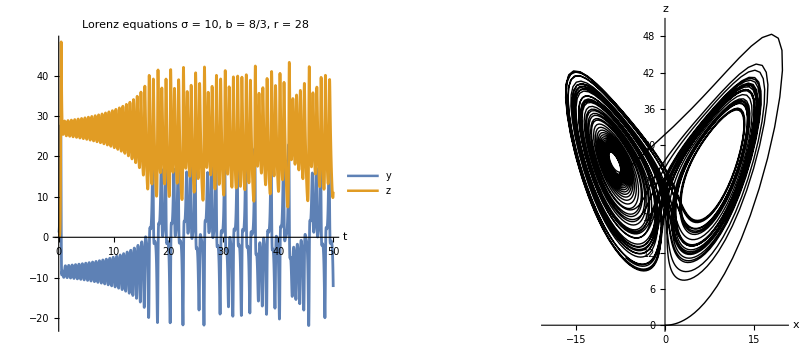

/Users/emasroo1/Library/CloudStorage/GoogleDrive-emasroo1@swarthmore.edu/My Drive/Teaching/Spring 2025/E91/Homework/HW7/lorenzr28.pdf

```mathematica
With[{finaltime=50,sol=sol1},GraphicsRow@{Plot[{y[t]/.sol,z[t]/.sol},{t,0,finaltime},PlotLegends->Placed[LineLegend[style[#,18]&/@{"y","z"},LegendLayout->"Row"],{0.5,0.9}],ImageSize->{400,160},PlotStyle->Thickness[0.005],AxesLabel->{style["t",18],None},PlotLabel->style["Lorenz equations σ = 10, b = 8/3, r = 28",18]],ParametricPlot[{x[t]/.sol,z[t]/.sol},{t,0,finaltime},ImageSize->{240,300},PlotStyle->Directive[Black,Thin],PlotRange->{{-20,20},{0,50}},AxesLabel->(style[#,18]&/@{"x","z"}),PlotPoints->60]}
]
Export[NotebookDirectory[]<>"lorenzr28.pdf",%]
```

#### Case 1 r = 21.5

```mathematica
sol2=With[{σval=10,bval=8/3,rval=21.5},NDSolve[{eq1,eq2,eq3,x[0]==0,y[0]==1,z[0]==20}/.{r->rval,σ->σval,b->bval},{x,y,z},{t,0,100}]][[1]];
```

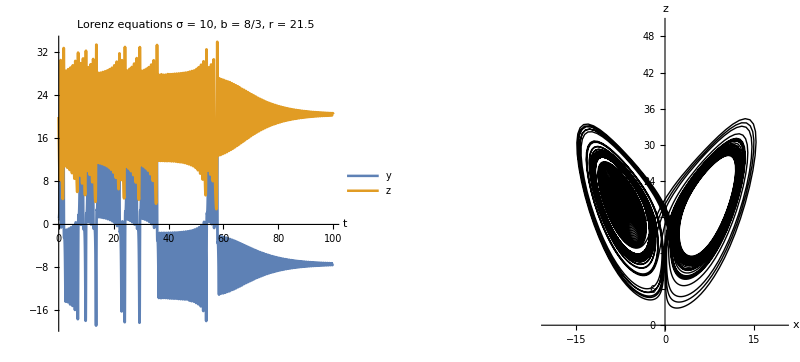

/Users/emasroo1/Library/CloudStorage/GoogleDrive-emasroo1@swarthmore.edu/My Drive/Teaching/Spring 2025/E91/Homework/HW7/lorenzr21.5.pdf

```mathematica
With[{finaltime=100,sol=sol2},GraphicsRow@{Plot[{y[t]/.sol,z[t]/.sol},{t,0,finaltime},PlotLegends->Placed[LineLegend[style[#,18]&/@{"y","z"},LegendLayout->"Row"],{0.5,0.9}],ImageSize->{400,160},PlotStyle->Thickness[0.005],AxesLabel->{style["t",18],None},PlotLabel->style["Lorenz equations σ = 10, b = 8/3, r = 21.5",18]],ParametricPlot[{x[t]/.sol,z[t]/.sol},{t,0,finaltime},ImageSize->{240,300},PlotStyle->Directive[Black,Thin],PlotRange->{{-20,20},{0,50}},AxesLabel->(style[#,18]&/@{"x","z"}),PlotPoints->120]}
]
Export[NotebookDirectory[]<>"lorenzr21.5.pdf",%]
```

#### Case 2 r = 14

```mathematica
sol3=With[{σval=10,bval=8/3,rval=14},NDSolve[{eq1,eq2,eq3,x[0]==0,y[0]==1,z[0]==0}/.{r->rval,σ->σval,b->bval},{x,y,z},{t,0,100}]][[1]];
```

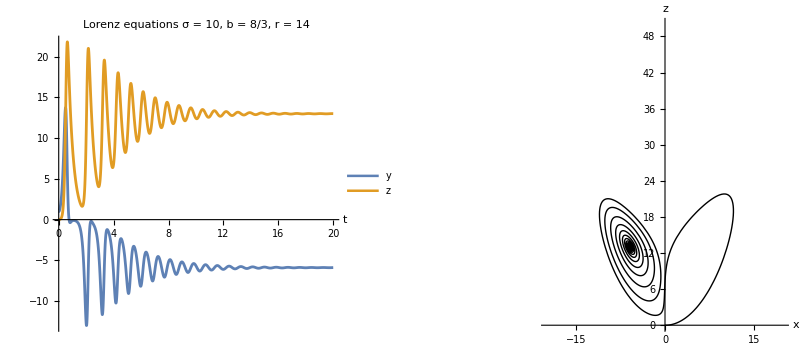

/Users/emasroo1/Library/CloudStorage/GoogleDrive-emasroo1@swarthmore.edu/My Drive/Teaching/Spring 2025/E91/Homework/HW7/lorenzr14.pdf

```mathematica
With[{finaltime=20,sol=sol3},GraphicsRow@{Plot[{y[t]/.sol,z[t]/.sol},{t,0,finaltime},PlotLegends->Placed[LineLegend[style[#,18]&/@{"y","z"},LegendLayout->"Row"],{0.5,0.9}],ImageSize->{400,160},PlotStyle->Thickness[0.005],AxesLabel->{style["t",18],None},PlotLabel->style["Lorenz equations σ = 10, b = 8/3, r = 14",18]],ParametricPlot[{x[t]/.sol,z[t]/.sol},{t,0,finaltime},ImageSize->{240,300},PlotStyle->Directive[Black,Thin],PlotRange->{{-20,20},{0,50}},AxesLabel->(style[#,18]&/@{"x","z"})]}
]
Export[NotebookDirectory[]<>"lorenzr14.pdf",%]
```

## Eigenvalues

```mathematica
f[x_,y_,z_]:=σ(y-x)
g[x_,y_,z_]:=r x - y - x z
h[x_,y_,z_]:=x y-b z
```

```mathematica
jacmat=D[{f[x,y,z],g[x,y,z],h[x,y,z]},{{x,y,z}}]
```

{{-σ,σ,0},{r-z,-1,-x},{y,x,-b}}

```mathematica
MatrixForm@jacmat
```

(-σ | σ | 0
r-z | -1 | -x
y | x | -b)

```mathematica
jacmat/.{x->0,y->0,z->0}
MatrixForm@%
```

{{-σ,σ,0},{r,-1,0},{0,0,-b}}

(-σ | σ | 0
r | -1 | 0
0 | 0 | -b)

```mathematica
Eigenvalues[jacmat/.{x->0,y->0,z->0}]
%/.σ->10
```

{-b,1/2 (-1-σ-√(1-2 σ+4 r σ+σ^2)),1/2 (-1-σ+√(1-2 σ+4 r σ+σ^2))}

{-b,1/2 (-11-√(81+40 r)),1/2 (-11+√(81+40 r))}

```mathematica
Solve[1-2 σ+4 r σ+σ^2==0,r][[1]]//Simplify
```

{r→-(-1+σ)^2/(4 σ)}

```mathematica
CharacteristicPolynomial[jacmat/.{x->0,y->0,z->0},λ]
```

(-b-λ) (λ+λ^2+σ-r σ+λ σ)

```mathematica
(jacmat/.{x->0,y->0,z->0})-λ IdentityMatrix[3]
```

{{-λ-σ,σ,0},{r,-1-λ,0},{0,0,-b-λ}}

```mathematica
Det[(jacmat/.{x->0,y->0,z->0})-λ IdentityMatrix[3]]
```

(-b-λ) (λ+λ^2+σ-r σ+λ σ)

So one eigenvalue is -b, and the other can be found by solving a quadratic equation.

```mathematica
λ^2+λ (σ+1)+σ-r σ
```

λ^2+σ-r σ+λ (1+σ)

```mathematica
Manipulate[λ/.Solve[λ^2+λ (σ+1)+σ-r σ==0,λ]/.σ->10/.r->rval,{rval,0.1,30}]
```

```mathematica
Manipulate[Eigenvalues[jacmat/.{x->0,y->0,z->0}/.σ->10/.r->rval/.b->8/3],{rval,0.1,30}]
```

```mathematica
Manipulate[StreamPlot[{f[x,y,0],g[x,y,0]}/.{σ->10,b->8/3,r->rval},{x,-20,20},{y,-20,20},PlotRangePadding->None],{rval,0.1,30}]
```

#### Solve equation

```mathematica
Solve[{f[x,y,z],g[x,y,z],h[x,y,z]}=={0,0,0},{x,y,z}]
```

{{x→0,y→0,z→0},{x→-√b √(-1+r),y→-√b √(-1+r),z→-1+r},{x→√b √(-1+r),y→√b √(-1+r),z→-1+r}}

So C- and C+ are the 2nd and third solutions here.

```mathematica
%62[[2]]
```

{x→-√b √(-1+r),y→-√b √(-1+r),z→-1+r}

```mathematica
%62[[1]]
```

{x→0,y→0,z→0}

```mathematica
jacmat/.%62[[2]]
MatrixForm@%
```

{{-σ,σ,0},{1,-1,√b √(-1+r)},{-√b √(-1+r),-√b √(-1+r),-b}}

(-σ | σ | 0
1 | -1 | √b √(-1+r)
-√b √(-1+r) | -√b √(-1+r) | -b)

```mathematica
CharacteristicPolynomial[jacmat/.%62[[2]],λ]
```

-b r λ-λ^2-b λ^2-λ^3+2 b σ-2 b r σ-b λ σ-λ^2 σ

```mathematica
CharacteristicPolynomial[jacmat/.%62[[1]],λ]
```

(-b-λ) (λ+λ^2+σ-r σ+λ σ)

```mathematica
CharacteristicPolynomial[jacmat/.%62[[3]],λ]
```

-b r λ-λ^2-b λ^2-λ^3+2 b σ-2 b r σ-b λ σ-λ^2 σ

```mathematica
CharacteristicPolynomial[jacmat/.%62[[2]],λ]/.{r->3,σ->10,b->8/3}
```

-320/3-(104 λ)/3-(41 λ^2)/3-λ^3

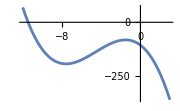

```mathematica
Plot[Evaluate[CharacteristicPolynomial[jacmat/.%62[[2]],λ]/.{r->3,σ->10,b->8/3}],{λ,-12,3},ImageSize->Small]
```

```mathematica
Manipulate[Plot[Evaluate[CharacteristicPolynomial[jacmat/.%62[[2]],λ]/.{r->rval,σ->10,b->8/3}],{λ,-12,3},ImageSize->Small],{rval,1,30}]
```

```mathematica
Eigenvalues[(jacmat/.%62[[2]]/.b->8/3/.σ->10/.r->3)]
```

{1/3 Root-34.4Root[2880+312 #1+41 #1^2+#1^3&,1]-34.35896524813004,1/3 Root-3.32+8.53 ⅈRoot[2880+312 #1+41 #1^2+#1^3&,3]-3.320517375934981,1/3 Root-3.32-8.53 ⅈRoot[2880+312 #1+41 #1^2+#1^3&,2]-3.320517375934981}

Solving this equation is too hard even for Mathematica, and gives really long expressions. Let’s use Strogatz’s hint:

```mathematica
Solve[(CharacteristicPolynomial[jacmat/.%62[[2]],λ]/.λ->I ω)==0,ω]
```

{{ω→1/3 ⅈ (1+b+σ)+(ⅈ 2^(1/3) (-(1+b+σ)^2+3 (b r+b σ)))/(3 (-2-6 b-6 b^2-2 b^3+9 b r+9 b^2 r-6 σ+51 b σ+3 b^2 σ-45 b r σ-6 σ^2+3 b σ^2-2 σ^3+√((-2-6 b-6 b^2-2 b^3+9 b r+9 b^2 r-6 σ+51 b σ+3 b^2 σ-45 b r σ-6 σ^2+3 b σ^2-2 σ^3)^2+4 (-(1+b+σ)^2+3 (b r+b σ))^3))^(1/3))-1/(3 2^(1/3))ⅈ (-2-6 b-6 b^2-2 b^3+9 b r+9 b^2 r-6 σ+51 b σ+3 b^2 σ-45 b r σ-6 σ^2+3 b σ^2-2 σ^3+√((-2-6 b-6 b^2-2 b^3+9 b r+9 b^2 r-6 σ+51 b σ+3 b^2 σ-45 b r σ-6 σ^2+3 b σ^2-2 σ^3)^2+4 (-(1+b+σ)^2+3 (b r+b σ))^3))^(1/3)},{ω→1/3 ⅈ (1+b+σ)-(ⅈ (1+ⅈ √3) (-(1+b+σ)^2+3 (b r+b σ)))/(3 2^(2/3) (-2-6 b-6 b^2-2 b^3+9 b r+9 b^2 r-6 σ+51 b σ+3 b^2 σ-45 b r σ-6 σ^2+3 b σ^2-2 σ^3+√((-2-6 b-6 b^2-2 b^3+9 b r+9 b^2 r-6 σ+51 b σ+3 b^2 σ-45 b r σ-6 σ^2+3 b σ^2-2 σ^3)^2+4 (-(1+b+σ)^2+3 (b r+b σ))^3))^(1/3))+1/(6 2^(1/3))ⅈ (1-ⅈ √3) (-2-6 b-6 b^2-2 b^3+9 b r+9 b^2 r-6 σ+51 b σ+3 b^2 σ-45 b r σ-6 σ^2+3 b σ^2-2 σ^3+√((-2-6 b-6 b^2-2 b^3+9 b r+9 b^2 r-6 σ+51 b σ+3 b^2 σ-45 b r σ-6 σ^2+3 b σ^2-2 σ^3)^2+4 (-(1+b+σ)^2+3 (b r+b σ))^3))^(1/3)},{ω→1/3 ⅈ (1+b+σ)-(ⅈ (1-ⅈ √3) (-(1+b+σ)^2+3 (b r+b σ)))/(3 2^(2/3) (-2-6 b-6 b^2-2 b^3+9 b r+9 b^2 r-6 σ+51 b σ+3 b^2 σ-45 b r σ-6 σ^2+3 b σ^2-2 σ^3+√((-2-6 b-6 b^2-2 b^3+9 b r+9 b^2 r-6 σ+51 b σ+3 b^2 σ-45 b r σ-6 σ^2+3 b σ^2-2 σ^3)^2+4 (-(1+b+σ)^2+3 (b r+b σ))^3))^(1/3))+1/(6 2^(1/3))ⅈ (1+ⅈ √3) (-2-6 b-6 b^2-2 b^3+9 b r+9 b^2 r-6 σ+51 b σ+3 b^2 σ-45 b r σ-6 σ^2+3 b σ^2-2 σ^3+√((-2-6 b-6 b^2-2 b^3+9 b r+9 b^2 r-6 σ+51 b σ+3 b^2 σ-45 b r σ-6 σ^2+3 b σ^2-2 σ^3)^2+4 (-(1+b+σ)^2+3 (b r+b σ))^3))^(1/3)}}

```mathematica
Eigenvalues[jacmat/.%62[[2]]]
```

{Root[-2 b σ+2 b r σ+(b r+b σ) #1+(1+b+σ) #1^2+#1^3&,1],Root[-2 b σ+2 b r σ+(b r+b σ) #1+(1+b+σ) #1^2+#1^3&,2],Root[-2 b σ+2 b r σ+(b r+b σ) #1+(1+b+σ) #1^2+#1^3&,3]}

```mathematica
Solve[CharacteristicPolynomial[jacmat/.%62[[2]]/.b->3/.σ->10,λ]==0,λ]
```

{{λ→-14/3+(-106+9 r)/(3 (44+621 r+9 √(-14680+4420 r+4443 r^2+9 r^3))^(1/3))-1/3 (44+621 r+9 √(-14680+4420 r+4443 r^2+9 r^3))^(1/3)},{λ→-14/3-((1+ⅈ √3) (-106+9 r))/(6 (44+621 r+9 √(-14680+4420 r+4443 r^2+9 r^3))^(1/3))+1/6 (1-ⅈ √3) (44+621 r+9 √(-14680+4420 r+4443 r^2+9 r^3))^(1/3)},{λ→-14/3-((1-ⅈ √3) (-106+9 r))/(6 (44+621 r+9 √(-14680+4420 r+4443 r^2+9 r^3))^(1/3))+1/6 (1+ⅈ √3) (44+621 r+9 √(-14680+4420 r+4443 r^2+9 r^3))^(1/3)}}

#### Two-dimensional Jacobian

```mathematica
jacmat[[1;;2,1;;2]]/.{x->0,y->0,z->0}
MatrixForm@%
```

{{-σ,σ},{r,-1}}

(-σ | σ
r | -1)

```mathematica
Eigenvalues[jacmat[[1;;2,1;;2]]/.{x->0,y->0,z->0}]/.σ->10/.r->1.4
```

{-11.3523,0.35235}

```mathematica
CharacteristicPolynomial[jacmat[[1;;2,1;;2]],λ]
```

λ+λ^2+σ-r σ+z σ+λ σ

```mathematica
Solve[0==CharacteristicPolynomial[jacmat[[1;;2,1;;2]]/.{x->0,y->0,z->0},λ],λ]
```

{{λ→1/2 (-1-σ-√(1-2 σ+4 r σ+σ^2))},{λ→1/2 (-1-σ+√(1-2 σ+4 r σ+σ^2))}}

```mathematica
CharacteristicPolynomial[jacmat,λ]
```

x (-x λ-x σ-y σ)+(-b-λ) (λ+λ^2+σ-r σ+z σ+λ σ)

```mathematica
Solve[0==CharacteristicPolynomial[jacmat,λ]]
```

{{y→(-b λ-x^2 λ-λ^2-b λ^2-λ^3-b σ+b r σ-x^2 σ-b z σ-λ σ-b λ σ+r λ σ-z λ σ-λ^2 σ)/(x σ)},{b→-λ,x→0},{x→0,z→(-λ-λ^2-σ+r σ-λ σ)/σ},{λ→0,σ→0},{x→-ⅈ √(1+λ) √(b+λ),σ→0},{x→ⅈ √(1+λ) √(b+λ),σ→0}}